```mathematica
mub[sqrts_]:=1303/(1+0.286*sqrts)*1.33;
```

```mathematica
mub[200]
```

29.7765

```mathematica
mub[62.4]
```

91.9534

```mathematica
mub[39]
```

142.586

```mathematica
mub[27]
```

198.692

```mathematica
mub[19.6]
```

262.352

```mathematica
mub[11.5]
```

404.055

```mathematica
mub[7.7]
```

541.187

-2.50019

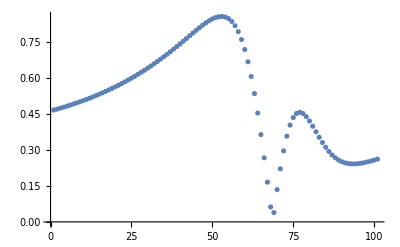

{{169}}

```mathematica
mub=541;
chi1mub[mub_]:=Import[NotebookDirectory[]<>"mub"<>ToString[mub]<>"/final/buffer/chi1.dat"]
chi2mub[mub_]:=Import[NotebookDirectory[]<>"mub"<>ToString[mub]<>"/final/buffer/chi2.dat"]
chi3mub[mub_]:=Import[NotebookDirectory[]<>"mub"<>ToString[mub]<>"/final/buffer/chi3.dat"]
chi4mub[mub_]:=Import[NotebookDirectory[]<>"mub"<>ToString[mub]<>"/final/buffer/chi4.dat"]
T=Table[i,{i,90,300}];
chi1=Flatten[chi1mub[mub]];
chi2=Flatten[chi2mub[mub]];
chi3=Flatten[chi3mub[mub]];
chi4=Flatten[chi4mub[mub]];
r32=chi3/chi2;
r21=chi2/chi1;
r42=chi4/chi2;
dr32=Table[Abs[r32[[i]]-0.60824],{i,100,200}];
r42[[169]]
ListPlot[{dr32}]
mindr32=Min[dr32];
Position[dr32,mindr32]+100
```